Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{σ→1.95132×10^-26 (-2.21071×10^25-1.61436×10^24 wf3-1.16772×10^23 wfres-5.37592×10^-13 √(1.87328×10^75-1.67153×10^74 wf3+9.01765×10^72 wf3^2+4.31994×10^74 wfres+1.30456×10^72 wf3 wfres+4.71819×10^70 wfres^2))},{σ→1.95132×10^-26 (-2.21071×10^25-1.61436×10^24 wf3-1.16772×10^23 wfres+5.37592×10^-13 √(1.87328×10^75-1.67153×10^74 wf3+9.01765×10^72 wf3^2+4.31994×10^74 wfres+1.30456×10^72 wf3 wfres+4.71819×10^70 wfres^2))}}

1.95132×10^-26 (-2.21071×10^25-1.61436×10^24 wf3-1.16772×10^23 wfres+5.37592×10^-13 √(1.87328×10^75-1.67153×10^74 wf3+9.01765×10^72 wf3^2+4.31994×10^74 wfres+1.30456×10^72 wf3 wfres+4.71819×10^70 wfres^2))

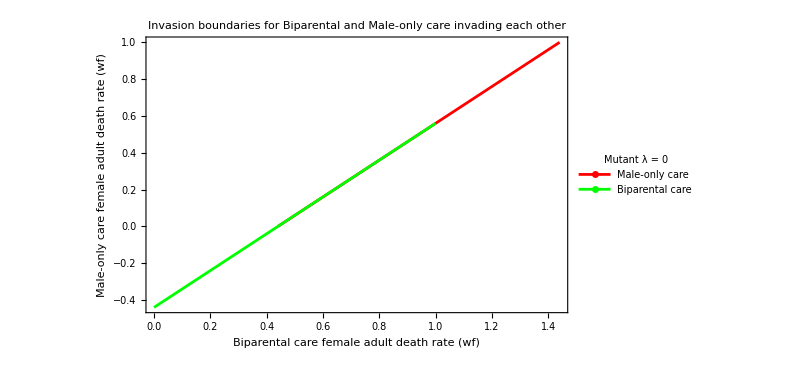

```mathematica
(*16th Jan 2024, defining trade-offs and parameter values outside of the params1 function*)

(*BASELINES*)
em0=0.75;
ef = 1-em0;
(*Now using numbers from literature justifications*)
mum0=0.5;
muf0= 0.5;

sigjm0=0.6;
sigjf0=0.6;
taum0=0.1;
tauf0=0.1;

mm0=0.5;
mf0=0.5;

k0=250;
rr0=6;
wm0=0.4;
wf0=0.4;

z0=1;
(*_________________________________________________________________________*)
(*RESIDENTS*)


(*Male only care*)

emres=em0;
efres =1-em0;
zres = z0;
cmres = 0.7;
cfres = 0.0;
ctres = cmres+cfres;

mumres=mum0*E^(-zres*ctres);
mufres=muf0*E^(-zres*ctres);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;

mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
wmres=1-((1-wm0)*E^(-cmres));
(*wfres= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres)));*)

KR=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

emmres = emres*(1-mumres)*mmres;
emfres = efres* (1-mufres)*mfres;
esmres= emres*(1-mumres);
esfres = efres* (1-mufres);
amres = emres*(1-mumres)*mmres*sigjmres;
afres = efres* (1-mufres)* mfres*sigjfres;

AR =KR*(1-((wmres*amres+wfres*afres)*(mumres*emres + mufres*efres + mmres*esmres + mfres*esfres)/((emmres*sigjmres+emfres*sigjfres)*rres*afres)));




(*Female only*)
emres=em0;
efres =1-emres;

zres = z0;
cmres2 = 0.0;
cfres2 = 0.7;
ctres2 = cmres2+cfres2;

mumres2=mum0*E^(-zres*ctres2);
mufres2=muf0*E^(-zres*ctres2);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
KR2=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres2=1-((1-wm0)*E^(-cmres2));
wfres2= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres2)));

emmres2 = emres*(1-mumres2)*mmres;
emfres2 = efres* (1-mufres2)*mfres;
esmres2= emres*(1-mumres2);
esfres2 = efres* (1-mufres2);
amres2 = emres*(1-mumres2)*mmres*sigjmres;
afres2 = efres* (1-mufres2)* mfres*sigjfres;

AR2 =KR2*(1-((wmres2*amres2+wfres2*afres2)*(mumres2*emres + mufres2*efres + mmres*esmres2 + mfres*esfres2)/((emmres2*sigjmres+emfres2*sigjfres)*rres*afres2)));


(*USE, wf*)

(*Biparental*)
emres=em0;
efres =1-emres;

zres = z0;
cmres3 = 0.35;
cfres3 = 0.35;
ctres3 = cmres3+cfres3;

mumres3=mum0*E^(-zres*ctres3);
mufres3=muf0*E^(-zres*ctres3);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));
KR3=k0;
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres3=1-((1-wm0)*E^(-cmres3));
(*wfres3= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres3)));*)

emmres3 = emres*(1-mumres3)*mmres;
emfres3 = efres* (1-mufres3)*mfres;
esmres3= emres*(1-mumres3);
esfres3 = efres* (1-mufres3);
amres3 = emres*(1-mumres3)*mmres*sigjmres;
afres3 = efres* (1-mufres3)* mfres*sigjfres;

AR3 =KR3*(1-((wmres3*amres3+wfres3*afres3)*(mumres3*emres + mufres3*efres + mmres*esmres3 + mfres*esfres3)/((emmres3*sigjmres+emfres3*sigjfres)*rres*afres3)));




(*No care*)

emres=em0;
efres =1-emres;

zres = z0;
cmres4 = 0.0;
cfres4 = 0.0;
ctres4 = cmres4+cfres4;

mumres4=mum0*E^(-zres*ctres4);
mufres4=muf0*E^(-zres*ctres4);

sigjmres=sigjm0;
sigjfres=sigjf0;
taumres=taum0;
taufres =tauf0;
mmres=1-((1-mm0)*E^(-((1-mum0)*emres)));
mfres=1-((1-mf0)*E^(-((1-muf0)*efres)));

KR4=k0;
(*KR=k0; for the purpose of boundary code this needs to be just a parameter i think? will it work to have AR4 as an alegbraic equation?*)
rres=rr0*E^(-((1-mum0)*emres+((1-muf0)*efres))/2);

wmres4=1-((1-wm0)*E^(-cmres4));
wfres4= 1-((1-wf0)*E^(-(efres*(1-muf0)+(1-mum0)*emres+cfres4)));

emmres4 = emres*(1-mumres4)*mmres;
emfres4= efres* (1-mufres4)*mfres;
esmres4= emres*(1-mumres4);
esfres4 = efres* (1-mufres4);
amres4 = emres*(1-mumres4)*mmres*sigjmres;
afres4 = efres* (1-mufres4)* mfres*sigjfres;

AR4 =KR4*(1-((wmres4*amres4+wfres4*afres4)*(mumres4*emres + mufres4*efres + mmres*esmres4 + mfres*esfres4)/((emmres4*sigjmres+emfres4*sigjfres)*rres*afres4)));
AR4;






(*___________________________________________________*)
(*MUTANTS*)

(*Male only care*)
z=z0;
cm4=0.7;
cf4=0.0;
ct4 = cm4 + cf4;

mum4=mum0*E^(-z*ct4);
muf4=muf0*E^(-z*ct4);

em=em0;
ef = 1-em0;
sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));
k4=k0; 
rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);

wm4=1-((1-wm0)*E^(-cm4));
(*wf4=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf4)));*)

emm4 = em*(1-mum4)*mm;
emf4 = ef* (1-muf4)*mf;
esm4= em*(1-mum4);
esf4 = ef*(1-muf4);
am4 = em*(1-mum4)*mm*sigjm;
af4= ef* (1-muf4)* mf*sigjf;

(*Female only care*)
z=z0;
cm2=0.0;
cf2=0.7;
ct2 = cm2 + cf2;
ct2;
em=em0;
ef = 1-em;

mum2=mum0*E^(-z*ct2);
muf2=muf0*E^(-z*ct2);

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));

k=k0;
rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);

wm2=1-((1-wm0)*E^(-cm2));
wf2=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf2)));

emm2 = em*(1-mum2)*mm;
emf2 = ef* (1-muf2)*mf;
esm2 = em*(1-mum2);
esf2 = ef*(1-muf2);
am2 = em*(1-mum2)*mm*sigjm;
af2 = ef* (1-muf2)* mf*sigjf;


(*Biparental care*)
z=z0;
cm3=0.35;
cf3=0.35;
ct3 = cm3 + cf3;
ct3;

em=em0;
ef=1-em;

mum3=mum0*E^(-z*ct3);
muf3=muf0*E^(-z*ct3);

wm3=1-((1-wm0)*E^(-cm3));
(*wf3=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf3)));*)

emm3 = em*(1-mum3)*mm;
emf3 = ef* (1-muf3)*mf;
esm3 = em*(1-mum3);
esf3 = ef*(1-muf3);
k=k0;

am3 = em*(1-mum3)*mm*sigjm;
af3 = ef* (1-muf3)* mf*sigjf;



(*No care*)

z=z0;
cm=0.0;
cf=0.0;
ct = cm + cf;

mum=mum0*E^(-z*ct);
muf=muf0*E^(-z*ct);

em=em0;
ef = 1-em0;

sigjm=sigjm0;
sigjf=sigjf0;
taum =taum0;
tauf=tauf0;
mm=1-((1-mm0)*E^(-((1-mum0)*em)));
mf=1-((1-mf0)*E^(-((1-muf0)*ef)));
rr=rr0*E^(-((1-mum0)*em+((1-muf0)*ef))/2);
k=k0;

wm=1-((1-wm0)*E^(-cm));
wf=1-((1-wf0)*E^(-(ef*(1-muf0)+(1-mum0)*em +cf)));

emm = em*(1-mum)*mm;
emf = ef* (1-muf)*mf;
esm = em*(1-mum);
esf = ef*(1-muf);
am = em*(1-mum)*mm*sigjm;
af = ef* (1-muf)* mf*sigjf;


AR3;





(*INVASION MATRICIES*)


(*Invading MALE only care*)
(*Male only care mutant*)
a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4);
b = rr*af4*(1-(AR/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat={{-λ+a,b},{c,-λ+d}};
MatrixForm[mat];


(*
(*Female only care mutant*)
a2=-(mum2*em+muf2*ef+mm*esm2+mf*esf2);
b2 = rr*af2*(1-(AR/k));
c2=emm2*sigjm*(1-λ*taum)+emf2*sigjf*(1-λ*tauf);
d2 = -(wm2*am2+wf2*af2);
mat2={{-λ+a2,b2},{c2,-λ+d2}};
MatrixForm[mat2];*)



(*Biparental care mutant
a3=-(mum3*em+muf3*ef+mm*esm3+mf*esf3);
b3 = rr*af3*(1-(AR/k));
c3=emm3*sigjm*(1-λ*taum)+emf3*sigjf*(1-λ*tauf);
d3 = -(wm3*am3+wf3*af3);
mat3={{-λ+a3,b3},{c3,-λ+d3}};
MatrixForm[mat3];*)


(*
(*No care mutant*)
a4=-(mum*em+muf*ef+mm*esm+mf*esf);
b4 = rr*af*(1-(AR/k));
c4=emm*sigjm*(1-λ*taum)+emf*sigjf*(1-λ*tauf);
d4= -(wm*am+wf*af);
mat4={{-λ+a4,b4},{c4,-λ+d4}};
MatrixForm[mat4];



(*Invading FEMALE only care*)
(*Male only mutant*)
(*a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4)*)
b02 = rr*af4*(1-(AR2/k));
(*c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4)*)
mat02={{-λ+a,b02},{c,-λ+d}};
MatrixForm[mat02];


(*Female only mutant*)
b22 = rr*af2*(1-(AR2/k));
mat22={{-λ+a2,b22},{c2,-λ+d2}};
MatrixForm[mat22];


(*Biparental mutant *)
b32 = rr*af3*(1-(AR2/k));
mat32={{-λ+a3,b32},{c3,-λ+d3}};
MatrixForm[mat32];


(*No care mutant*)
b42 = rr*af*(1-(AR2/k));
mat42={{-λ+a4,b42},{c4,-λ+d4}};
MatrixForm[mat42];



(*USE*)
(*Invading BIPARENTAL care*)
(*Male only mutant*)
b03 = rr*af4*(1-(AR3/k));
mat03={{-λ+a,b03},{c,-λ+d}};
MatrixForm[mat03];


(*Female only mutant*)
b23 = rr*af2*(1-(AR3/k));
mat23={{-λ+a2,b23},{c2,-λ+d2}};
MatrixForm[mat23];

(*Biparental mutant *)
b33 = rr*af3*(1-(AR3/k));
mat33={{-λ+a3,b33},{c3,-λ+d3}};
MatrixForm[mat33];

(*No care mutant*)
b43 = rr*af*(1-(AR3/k));
mat43={{-λ+a4,b43},{c4,-λ+d4}};
MatrixForm[mat43];



(*Invading NO CARE*)
(*Male only mutant*)

a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4);
b04 = rr*af4*(1-(AR4/k));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
mat={{-λ+a,b04},{c,-λ+d}};
MatrixForm[mat];

(*Female only mutant*)
b24 = rr*af2*(1-(AR4/k));
mat24={{-λ+a2,b24},{c2,-λ+d2}};
MatrixForm[mat24];

(*Biparental mutant *)
b34 = rr*af3*(1-(AR4/k));
mat34={{-λ+a3,b34},{c3,-λ+d3}};
MatrixForm[mat34];


(*No care mutant*)
b44 = rr*af*(1-(AR4/k));
mat44={{-λ+a4,b44},{c4,-λ+d4}};
MatrixForm[mat44];*)

(*Male only care invading biparental*)
b03 = rr*af4*(1-(AR3/k));
mat03={{-λ+a,b03},{c,-λ+d}};
MatrixForm[mat03];


(*want to use matrix 03 but the problem is the lambdas in all the other matrixes ? maybe put 03 at the end*)
(*Invading NO CARE resident*)
(*Male only mutant*)
(*Invading no care with male only,  made one thing (KR - carrying capacity) in AR4 continous*)
(*male only mutant matrix 0s but parameters all 4s, no care AR also 4*
a=-(mum4*em+muf4*ef+mm*esm4+mf*esf4);
b04= rr*af4*(1-(AR4/k4));
c=emm4*sigjm*(1-λ*taum)+emf4*sigjf*(1-λ*tauf);
d = -(wm4*am4+wf4*af4);
matMn={{-λ+a,b04},{c,-λ+d}};
MatrixForm[matMn]


Invading MALE ONLY resident*)
(*No care mutant*)
(*Invading male only care back with no care, for carrying capacities*)
(*no care mutant matrix 4s but parameters all 0s, male resident also 0AR
a4=-(mum*em+muf*ef+mm*esm+mf*esf);
b4 = rr*af*(1-(AR/k));
c4=emm*sigjm*(1-ϕ*taum)+emf*sigjf*(1-ϕ*tauf);
d4= -(wm*am+wf*af);
matNm={{-ϕ+a4,b4},{c4,-ϕ+d4}};
MatrixForm[matNm];*)



ans03=Solve[Det[mat03]==0,λ];
res03=λ/.ans03[[2]];

resMiB=Table[wf4=0.0+i/10;jo=
FindRoot[{res03==0},{wfres3,0.1,0.9}];{wfres3/.jo,wf4},{i,0,10}];


(*Biparental invades male only*)
(*Biparental care mutant*)
a3=-(mum3*em+muf3*ef+mm*esm3+mf*esf3);
b3 = rr*af3*(1-(AR/k));
c3=emm3*sigjm*(1-σ*taum)+emf3*sigjf*(1-σ*tauf);
d3 = -(wm3*am3+wf3*af3);
mat3={{-σ+a3,b3},{c3,-σ+d3}};
MatrixForm[mat3];


ans30=Solve[Det[mat3]==0,σ]
res30=σ/.ans30[[2]]
resBiM=Table[wf3=0.0+i/10;jo=
FindRoot[{res30==0},{wfres,0.1,0.9}];{wfres/.jo,wf3},{i,0,10}];



resBiMflip=Table[wf3=0.0+i/10;jo=
FindRoot[{res30==0},{wfres,0.1,0.9}];{wf3, wfres/.jo},{i,0,10}];



ListPlot[{Re[resMiB],Re[resBiMflip]},
Joined -> {True, True},
Frame -> True,
PlotLegends->LineLegend[{"Male-only care", "Biparental care"},
LegendLabel-> "Mutant λ = 0",
LegendMarkers->"Line" ,
LegendMarkerSize->10,
LabelStyle ->{FontSize->12}
],
FrameLabel->{"Biparental care female adult death rate (wf)",Rotate[Column[{"Male-only care female","adult death rate (wf)"},Alignment-> Center], 270 Degree]},
PlotLabel-> "Invasion boundaries for Biparental and Male-only care invading each other",LabelingSize->350,
ImageSize-> 600,
PlotStyle  -> {Red,Green}]
```